```mathematica
Integrate[(Pi/3)*9.81*(32-6*h^2+h^3),{h,2,4}]
```

123.276

```mathematica
Integrate[1/(x^2),{x,0.1,50.1}]
```

9.98004

```mathematica
f = Interpolation[{{0,0.00},{0.05,37},{0.1,71},{0.15,104},{0.20,134},{0.25,161},{0.30,185},{0.35,207},{0.40,225},{0.45,239},{0.50,250}}]
```

InterpolatingFunction[…]

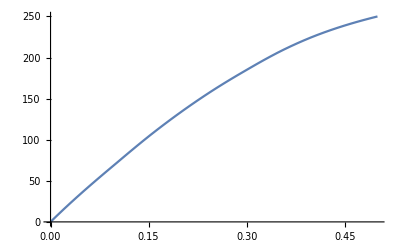

```mathematica
Plot[f[x],{x,0,0.5}]
```

```mathematica
NIntegrate[f[x],{x,0,0.5}]
```

74.5229

```mathematica
Series[f[x],{x,0.25,3}]
```

161.+510. (x-0.25)-600. (x-0.25)^2-2.6148×10^-11 (x-0.25)^3+O[x-0.25]^4